```mathematica
allosc=SortBy[First/@Map[MinimalBy[#,#InitialWeight&]&,Values@GroupBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period&]],#Period&];
```

### Functions to add to code-02

With active color:

```mathematica
ClearAll@CellularAutomatonInteractiveHistory
CellularAutomatonInteractiveHistory[rule_,init_,t_,opts___]:=
AnimationVideo[(ArrayPlot3D[
MapAt[#/. 1-> 2&, CellularAutomaton[rule,init,tt], -1],
ColorFunction->(If[#==1,SetAlphaChannel[RGBColor[1., 0.6436, 0.03622, 1.],1],If[# == 2, SetAlphaChannel[RGBColor[1., 0.4, 0.03622],1], Transparent]] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3],opts
]),{tt,0, t,1}]
```

To export:

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["hist2.mp4", CellularAutomatonHistory["GameOfLife",caax,60,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5}, Boxed->False]]*)
```

```mathematica
PatternsLayeredGraph[patterndata_, opts___]:= 
LayeredGraph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]], VertexShapeFunction->(With[{sa =SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#2[[-1]] ]]+ 1)->1]]}, Inset[
ArrayPlot[sa, Mesh->True,MeshStyle->Opacity[0.1], ImageSize->3Dimensions[sa]], #1]]&), opts]&@patterndata
```

```mathematica
BoundingBoxLayeredGraph[patterndata_, opts___]:= 
LayeredGraph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]], VertexShapeFunction->
Function[{pos, val, blah}, Rectangle[pos -Reverse[#] / 40 ,pos +Reverse[#] / 40]&@ (Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])], opts]&@ patterndata
```

### Square (Old)

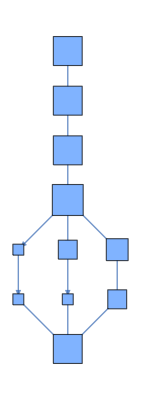

```mathematica
Graph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]],VertexSize->{x_:>(.25Sqrt[Times@@{Max[#[[2, 1]]  -  #[[2, 1]] ,1],Max[#[[2, 2]] - #[[2, 1]], 1]}&@CoordinateBounds[Last[x]]])}, VertexShapeFunction->"Square"]&/@ allosc[[{5}]]
```

### Layered with pattern

```mathematica
PatternsLayeredGraph@<|"Name"->"Rattlesnake","Year"->2016,"Class"->"Oscillator","Period"->11,"Wiki"->"https://conwaylife.com/wiki/Rattlesnake","DataFiles"->{"rattlesnake.cells","rattlesnake.rle"},"MatrixData"->SparseArray[…],"InitialWeight"->33|>
```

-Graphics-

More and larger plots, a bit memory-heavy:

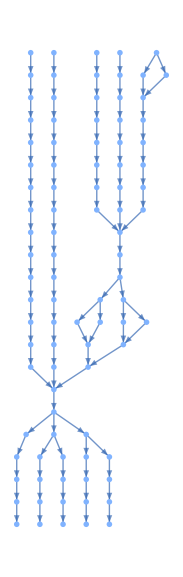
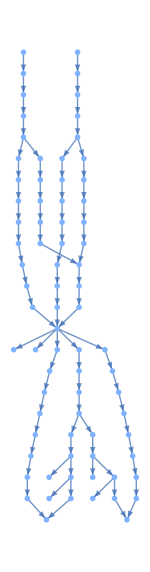
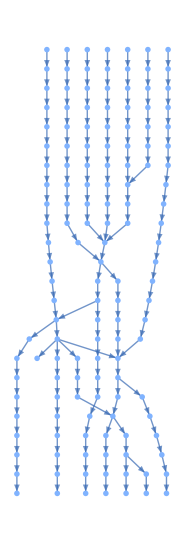
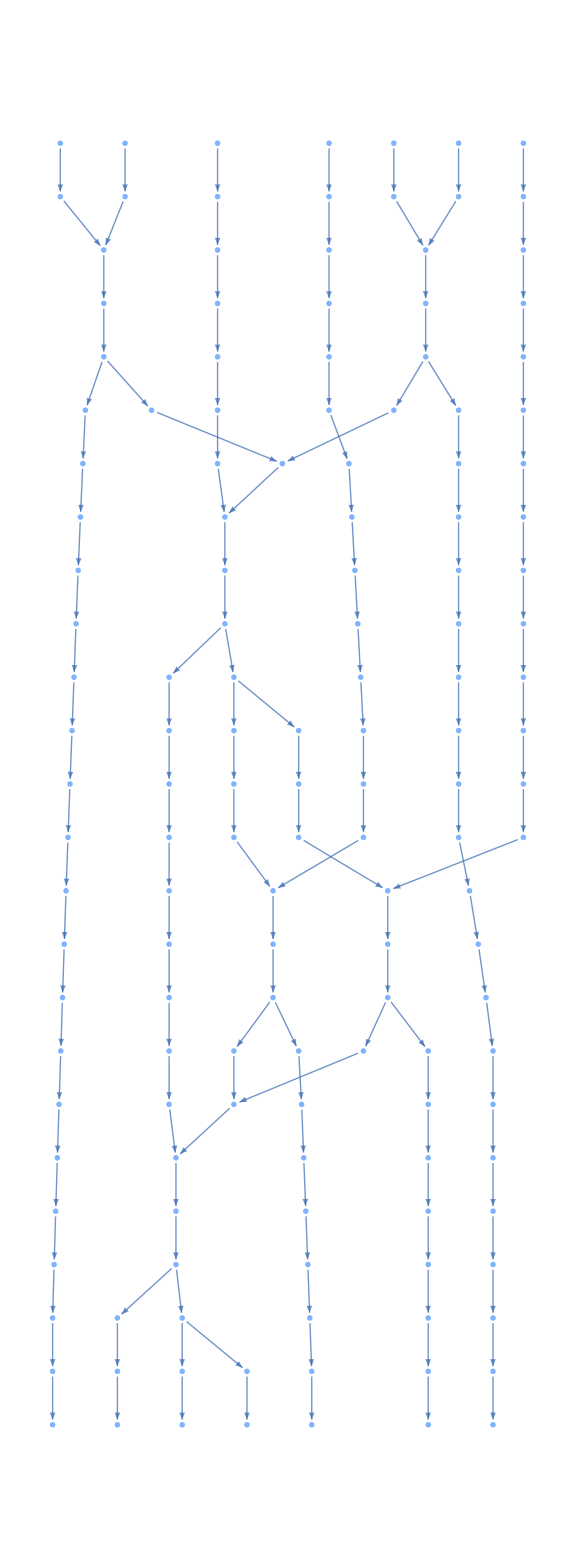
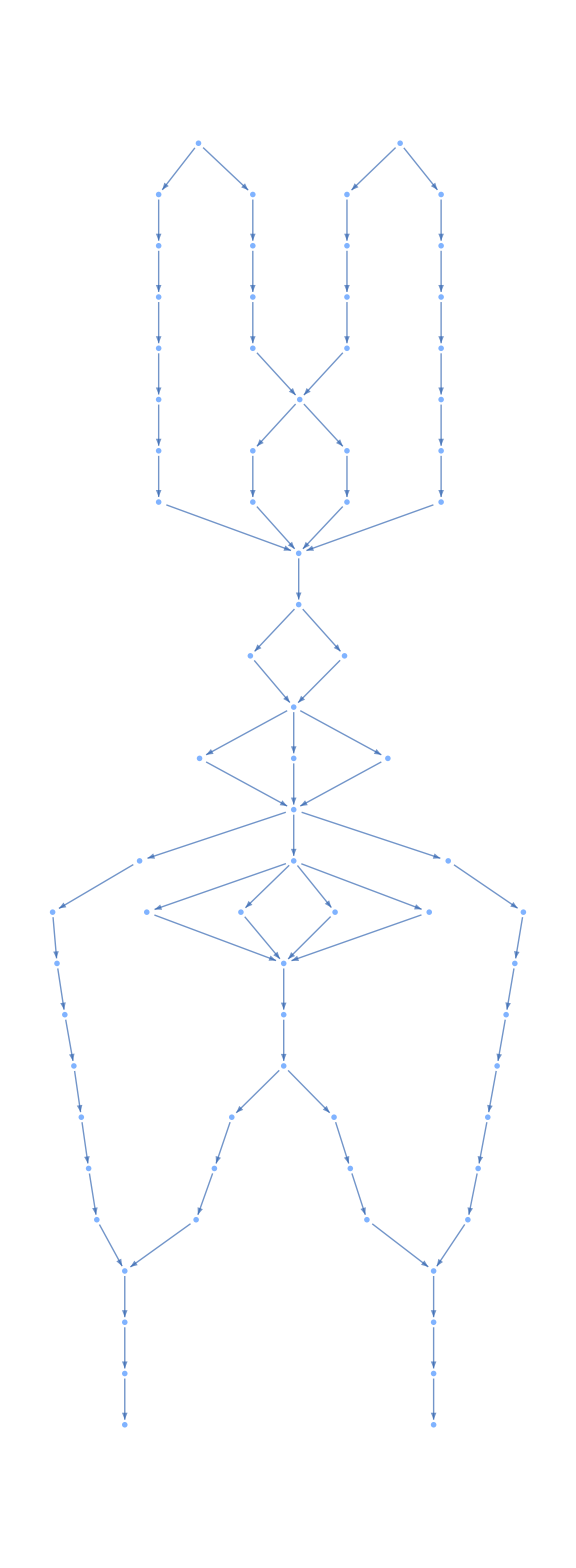
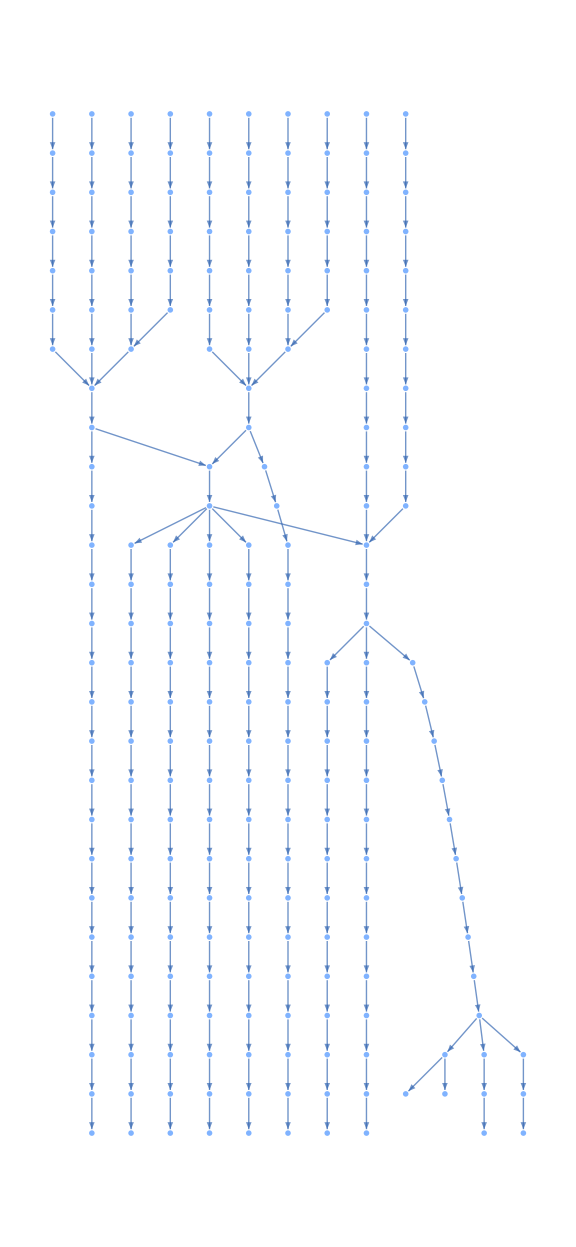

```mathematica
PatternsLayeredGraph[#, ImageSize->Large]&/@ Select[allosc[[20;;25]], KeyExistsQ[#, "MatrixData"]&]
```

### Bounding box layered

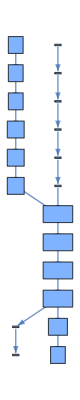

```mathematica
BoundingBoxLayeredGraph@ allosc[[10]]
```

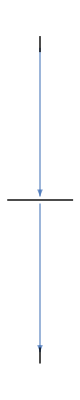
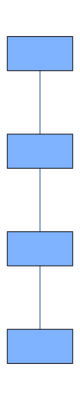
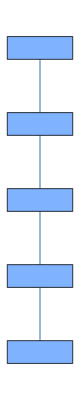
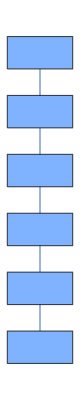
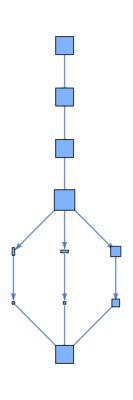
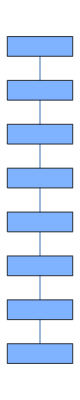
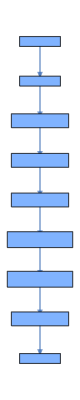
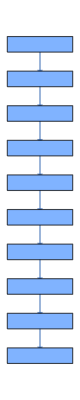
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BoundingBoxLayeredGraph[#]&/@ allosc[[;;30]]
```

### Trying to get fixed size to work

Kind of works, just need to center the graphs by shifting their embeddings

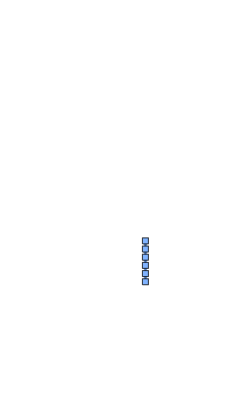
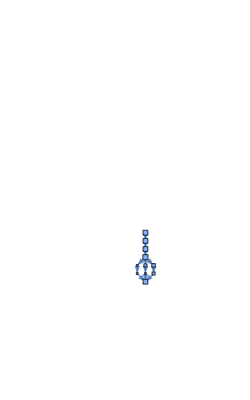
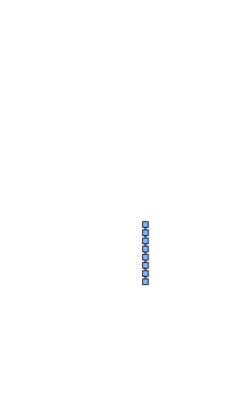
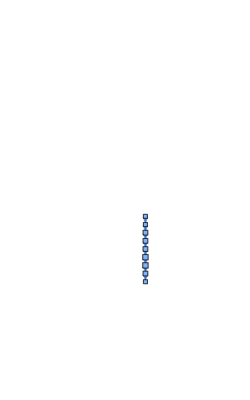
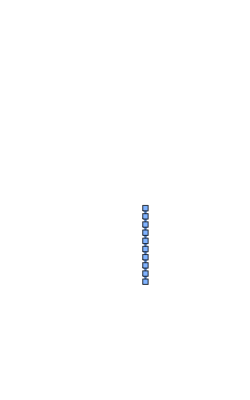
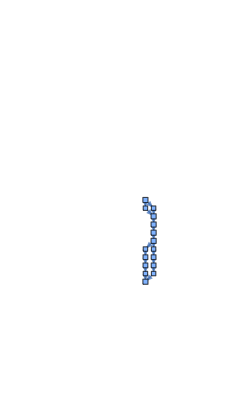
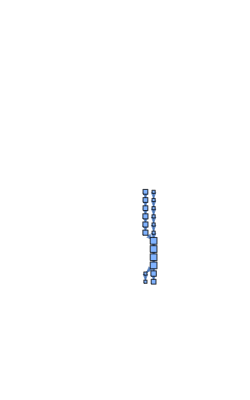
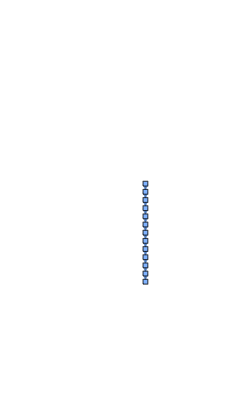
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphPlot[LayeredGraph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]],VertexSize->{x_:>(.25Sqrt[Times@@{Max[#[[2, 1]]  -  #[[2, 1]] ,1],Max[#[[2, 2]] - #[[2, 1]], 1]}&@CoordinateBounds[Last[x]]])}, VertexShapeFunction->"Square"], PlotRange->{{-15, 10}, {-10, 30}}]&/@ Take[allosc, 30]
```

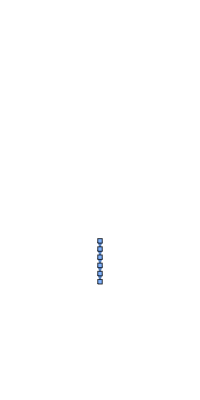
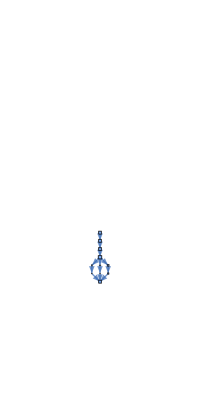
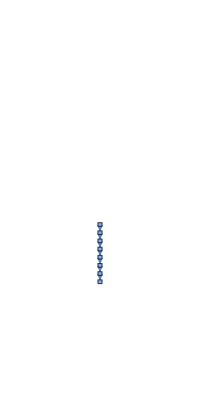
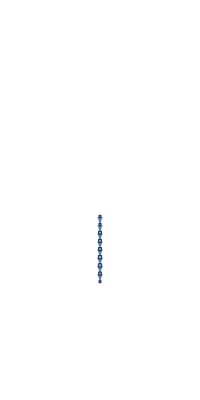
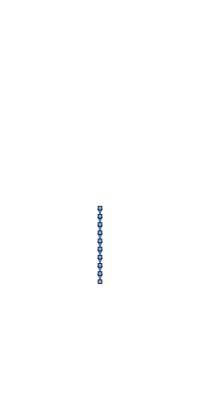
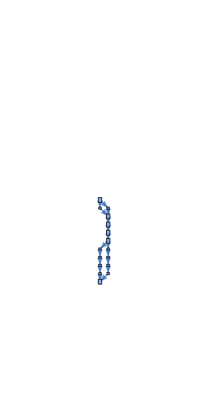
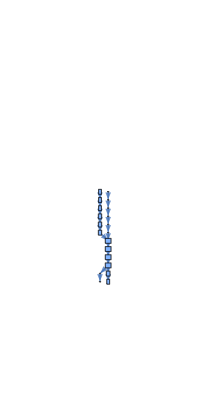
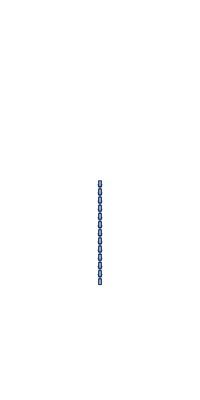
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphPlot[LayeredGraph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]], VertexShapeFunction->
Function[{pos, val, blah}, Rectangle[pos -Reverse[#] / 40 ,pos +Reverse[#] / 40]&@ (Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])]], PlotRange->{{-10, 10}, {-10, 30}}]&/@ Take[allosc, 30]
```

### Videos

#### With active color

```mathematica
ClearAll@CellularAutomatonHistory
CellularAutomatonHistory[rule_,init_,t_,opts___]:=
Table[(ArrayPlot3D[
MapAt[#/. 1-> 2&, CellularAutomaton[rule,init,tt], -1],
ColorFunction->(If[#==1,SetAlphaChannel[RGBColor[1., 0.6436, 0.03622, 1.],1],If[# == 2, SetAlphaChannel[RGBColor[1., 0.4, 0.03622],1], Transparent]] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3],opts
]),{tt,0, t,1}]
```

Regular from below

```mathematica
SetDirectory[NotebookDirectory[]];
Export["hist2.mp4", CellularAutomatonHistory["GameOfLife",caax,60,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5}, Boxed->False]]
```

hist2.mp4